## Beyond Mean Field Theoretical PDF for 2D Rayleigh-Levy flights

We derive the PDF of the density for a Rayleigh Levy flights in 2D, focusing on a correlation ξ~1/r^(1/2) (α=3/2=-n) and a Gaussian filter C_0(r)=C_0(x)C_0(y)=e^(-r^2/2)/2π. Notebook has three parts: a derivation of the cumulants, the skewness, and the density PDF.

### 1 Deriving the CGF

To derive the cumulants, we first specify a basis that is orthonormal with respect to the (Gaussian) window function. We resort to Laguerre polynomials, which are appropriately eigenfunctions of the 2D quantum harmonic oscillator:

```mathematica
𝒞0[r_]=(E^(-r^2/2))/(2π); (* the filter function *)
b[l_,r_]=LaguerreL[l,r^2/2]; (* basis function *)
```

The orthonormality is easy to show, e.g., up to l=8,

```mathematica
Lmax=8;
Table[If[q>=p,Integrate[2π r 𝒞0[r] b[q,r]b[p,r],{r,0,∞}],xx],{p,0,Lmax},{q,0,Lmax}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
xx | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
xx | xx | 1 | 0 | 0 | 0 | 0 | 0 | 0
xx | xx | xx | 1 | 0 | 0 | 0 | 0 | 0
xx | xx | xx | xx | 1 | 0 | 0 | 0 | 0
xx | xx | xx | xx | xx | 1 | 0 | 0 | 0
xx | xx | xx | xx | xx | xx | 1 | 0 | 0
xx | xx | xx | xx | xx | xx | xx | 1 | 0
xx | xx | xx | xx | xx | xx | xx | xx | 1)

The factor (2π)r in the integrand comes from the 2D polar coordinates Jacobian dV=2π r dr for spherically symmetric case.

Now the cumulants for the density PDF are derived by solving the following linear equation:

```mathematica
(* fix q=0 for simplicity; focus on ρ, not ∇ρ etc. *)
eqC31[LM_]:=Table[τ[p]==λ(Ξ[p,0]+∑_(q=0)^LM τ[q]/2 Ξ[p,q]),{p,0,LM}];
eqC33=φ[λ]==λ(1+τ[0]/2);
```

where the Ξ_(p p') are given by the integral

Ξ_(p p')=∫d^2 r d^2 r'b_p'(r)C_0(r)ξ(r-r')b_p'(r')C_0(r') .

We manage this in Fourier space, transforming the 4d integral into a one-dimensional integral.

We utilize Mathematica built-in functions for doing the Fourier transform:

```mathematica
FT2d[expr_]:=2π FourierTransform[expr,{x,y},{u,v}]/.{u->-u,v->-v}
IFT2d[expr_]:=1/(2π)FourierTransform[expr,{u,v},{x,y}]
```

Note: the FT’s are calculated in Cartesian coordinates for simplicity. For us, results always appear in the combination r^2=(x^1)^2+(x^1)^2. We can simply translate back to spherical coordinates after doing to FT.

We can test this with the two-point correlation function for α=3/2; or ξ(r)=1/r^(1/2):

```mathematica
R[x_,y_]=√(x^2+y^2);
ξf[x_,y_]=1/(√R[x,y]);

(* FT of correlation *)
ξt[k_]=Simplify[FT2d[ξf[x,y]]/.u^2+v^2->k^2,Assumptions->k>=0];
"ξ̃(k)"==ξt[k]
```

ξ̃(k)==(2 √2 π Gamma[3/4])/(k^(3/2) Gamma[1/4])

We can confirm that the FT and its inverse works properly by doing

```mathematica
"IFT[ FT[ ξ(r) ] ]"==Simplify[IFT2d[FT2d[ξf[x,y]]]/.x^2+y^2->r^2,Assumptions->r>=0]
```

IFT[ FT[ ξ(r) ] ]==1/(√r)

Clearly doing the transform and the inverse returns the function under study. We are now ready to calculate the Fourier transform of the basis multiplied by the filter. This is given by

```mathematica
(* FT of filter x basis *)
bt[l_,k_]:=Simplify[FT2d[𝒞0[R[x,y]]b[l,R[x,y]]]/.u^2->k^2-v^2,Assumptions->k>=0]
```

which happens to be analytical, e.g., up to l=6,

```mathematica
"b̃(k)"==(Table[bt[p,k],{p,0,6}]//MatrixForm)
```

b̃(k)==(ⅇ^(-k^2/2)
1/2 ⅇ^(-k^2/2) k^2
1/8 ⅇ^(-k^2/2) k^4
1/48 ⅇ^(-k^2/2) k^6
1/384 ⅇ^(-k^2/2) k^8
(ⅇ^(-k^2/2) k^10)/3840
(ⅇ^(-k^2/2) k^12)/46080)

The quantities Ξ_(p p') turn out to be expressible analytically; assuming the dependence of all components all falls into ξ_0=Ξ_00; another way of saying this is that we fix the normalization by using the numerical solution. We setup this computation below:

```mathematica
Ξ0[p_,q_]:=2π Integrate[k ξt[k]bt[p,k]bt[q,k],{k,0,∞}]
ΞTab[LM_]:=Table[Ξ0[p,q],{p,0,LM},{q,0,LM}];

(* fix L = LMax = 8 *)
L=8;
ΞTabL=ΞTab[L];
ΞTabL0=ΞTabL/ΞTabL[[1,1]]//FullSimplify;
ΞTabL0//TableForm
```

1 | 1/8 | 5/128 | 15/1024 | 195/32768 | 663/262144 | 4641/4194304 | 16575/33554432 | 480675/2147483648
1/8 | 5/64 | 45/1024 | 195/8192 | 3315/262144 | 13923/2097152 | 116025/33554432 | 480675/268435456 | 15862275/17179869184
5/128 | 45/1024 | 585/16384 | 3315/131072 | 69615/4194304 | 348075/33554432 | 3364725/536870912 | 15862275/4294967296 | 586904175/274877906944
15/1024 | 195/8192 | 3315/131072 | 23205/1048576 | 580125/33554432 | 3364725/268435456 | 37011975/4294967296 | 195634725/34359738368 | 8021023725/2199023255552
195/32768 | 3315/262144 | 69615/4194304 | 580125/33554432 | 16823625/1073741824 | 111035925/8589934592 | 1369443075/137438953472 | 8021023725/1099511627776 | 360946067625/70368744177664
663/262144 | 13923/2097152 | 348075/33554432 | 3364725/268435456 | 111035925/8589934592 | 821665845/68719476736 | 11229433215/1099511627776 | 72189213525/8796093022208 | 3537271462725/562949953421312
4641/4194304 | 116025/33554432 | 3364725/536870912 | 37011975/4294967296 | 1369443075/137438953472 | 11229433215/1099511627776 | 168441498225/17592186044416 | 1179090487575/140737488355328 | 62491795841475/9007199254740992
16575/33554432 | 480675/268435456 | 15862275/4294967296 | 195634725/34359738368 | 8021023725/1099511627776 | 72189213525/8796093022208 | 1179090487575/140737488355328 | 8927399405925/1125899906842624 | 508861766137725/72057594037927936
480675/2147483648 | 15862275/17179869184 | 586904175/274877906944 | 8021023725/2199023255552 | 360946067625/70368744177664 | 3537271462725/562949953421312 | 62491795841475/9007199254740992 | 508861766137725/72057594037927936 | 31040567734401225/4611686018427387904

We setup these values as rules that we can call to solve the cumulants up to a certain BMF order;

```mathematica
ΞRules0=Table[Ξ[p,q]->ξ0 ΞTabL0[[p+1,q+1]],{p,0,L},{q,0,L}];
ΞRulesUnion=Join@@ΞRules0;
```

Finally we can get the cumulants up to our desired order beyond mean field. We setup a function that does exactly this by solving the linear system of equation (equations C31 and C33 in https://arxiv.org/abs/2402.15915):

```mathematica
GetCGF[L_,λλ_,ξξ_]:=(eqC31sol0=Solve[eqC31[L]/.ΞRulesUnion,Table[τ[l],{l,0,L}]];eqC33[[2]]/.eqC31sol0[[1]]/.{λ[0]->λλ,ξ0->ξξ}//Simplify)
```

The CGFs up to a few orders beyond the mean field are e.g.,

```mathematica
(Table["φ(λ,ξ_0)"==GetCGF[p,λ,ξ],{p,0,6}]//TableForm)
```

φ(λ,ξ_0)==(2 λ)/(2-λ ξ)
φ(λ,ξ_0)==-(λ (-128+5 λ ξ))/(128-69 λ ξ+2 λ^2 ξ^2)
φ(λ,ξ_0)==-(λ (1048576-59680 λ ξ+225 λ^2 ξ^2))/(-1048576+583968 λ ξ-25569 λ^2 ξ^2+80 λ^3 ξ^3)
φ(λ,ξ_0)==-(λ (-68719476736+4671569920 λ ξ-37299300 λ^2 ξ^2+14625 λ^3 ξ^3))/(68719476736-39031308288 λ ξ+2074748004 λ^2 ξ^2-14061665 λ^3 ξ^3+4800 λ^4 ξ^4)
φ(λ,ξ_0)==λ-(1024 λ^2 ξ (562949953421312-37781803892736 λ ξ+391797834560 λ^2 ξ^2-397669050 λ^3 ξ^3+14625 λ^4 ξ^4))/(-1152921504606846976+663868804807262208 λ ξ-39716702778737664 λ^2 ξ^2+402382527169565 λ^3 ξ^3-407261589075 λ^4 ξ^4+14976000 λ^5 ξ^5)
φ(λ,ξ_0)==λ-(1024 λ^2 ξ (-604462909807314587353088+44179694383785383559168 λ ξ-592303447537800445952 λ^2 ξ^2+1126675495566659520 λ^3 ξ^3-157044410865225 λ^4 ξ^4+620568000 λ^5 ξ^5))/(1237940039285380274899124224-720224609357179819112005632 λ ξ+46757774087636437985918976 λ^2 ξ^2-609750899493143634092288 λ^3 ξ^3+1154215143929955873555 λ^4 ξ^4-160815636768056400 λ^5 ξ^5+635461632000 λ^6 ξ^6)
φ(λ,ξ_0)==-(λ (21267647932558653966460912964485513216-1841357243723911755436235099188756480 λ ξ+32653185473145388413675632691511296 λ^2 ξ^2-104731107955838903329156540661760 λ^3 ξ^3+36684418550785284649057786800 λ^4 ξ^4-727616515214386965974625 λ^5 ξ^5+334158507610200000 λ^6 ξ^6))/(-21267647932558653966460912964485513216+12475181210003238738666691581431513088 λ ξ-860772397805490476656025298869944320 λ^2 ξ^2+13375323546538215250071480888983552 λ^3 ξ^3-38420387057980693788755375430576 λ^4 ξ^4+12198699814946130775942450785 λ^5 ξ^5-221867659998992827684800 λ^6 ξ^6+94373677891584000 λ^7 ξ^7)

### 2 Skewness

The exact skewness for n=-α is given by

```mathematica
S3Th[n_]=3/2 Hypergeometric2F1[(2+n)/2,(2+n)/2,1,1/4]/.n->-3/2//N;
```

On the other hand, the one-point skewness of the density can be derived from the cumulants by a series expansion;

```mathematica
GetS3[k_]:=(cgf[λ_,ξ_]=GetCGF[k,λ,ξ];cgfExpand[λ_,ξ_]=Series[cgf[λ,ξ],{λ,0,3}]//Normal;c2=2!Coefficient[cgfExpand[λ,ξ],λ,2];c3=3!Coefficient[cgfExpand[λ,ξ],λ,3];S3=c3/c2^2//N;S3)
```

Using this, we can show that the beyond mean field prediction approaches the exact answer in an exponential fashion:

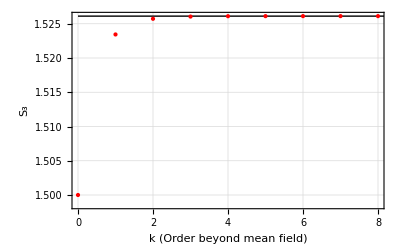

```mathematica
S3List=Table[{k,GetS3[k]},{k,0,8}];

ListPlot[S3List,Frame->True,PlotStyle->{Directive[Red,PointSize[Large]]},LabelStyle->Directive[FontFamily->"Helvetica",Medium],TicksStyle->Directive[FontFamily->"Helvetica",Medium],FrameLabel->{"k (Order beyond mean field)","S_3"},PlotRange->All,GridLines->Automatic,Epilog->{Directive[Black],Line[{{0,S3Th[n]},{Length[S3List],S3Th[n]}}/.n->3/2]}]
```

Clearly the beyond mean field solution quickly converges toward the exact answer.

### 3 PDF of the density

At mean field, the PDF of the density is given by

```mathematica
tPDFρ[ρ_,ξ0_]=(4 ⅇ^(-(2 (1+ρ))/ξ0) Hypergeometric0F1Regularized[2,(4 ρ)/ξ0^2])/ξ0^2;
```

Now that the cumulants are at hand, we can easily compute theoretical PDF of ρ beyond the mean field approximation. We take up to l=8 in the following, noting this can be extended to any order.

```mathematica
ϕBMF[λ_,ξ_]=GetCGF[8,λ,ξ]; (* change first argument to desired BMF order; L=0 is mean field *)
```

The way to the PDF is do an inverse Laplace transform. I setup a function doing a Riemann sum (of the inverse Laplace transform integral after one integration by parts) in the following:

```mathematica
ϕBMFρ[λ_,ξ_]=D[ϕBMF[λ,ξ], λ]//Simplify;
lmax=5000;dlstep=0.05;
tφ1[ξb_]=Table[{I λρ,ϕBMFρ[λρ I,ξb]Exp[ϕBMF[I λρ,ξb]]},{λρ,-lmax-dlstep/2,lmax+dlstep/2,dlstep}];
nPDFρ[ξ_,ρ_]:=(tφ1[ξ]/.{aa_,cc_}->1/ρ Exp[-aa ρ]cc/(2 Pi)  dlstep)//Total//Re;
```

We can show the BMF result compared with the theoretical (mean field) prediction:

```mathematica
Xi0=4.5; 
ρmin=10^-1;ρmax=20;Δρ=(ρmax-ρmin)/200;
nPDFρAtξ0=nPDFρ[Xi0,ρ];
tPDFρAtξ0=tPDFρ[ρ,Xi0];
BMFtoMF=Table[{ρ//N,nPDFρAtξ0/tPDFρAtξ0},{ρ,ρmin,ρmax,Δρ}]//Quiet;
```

The result is shown below (as a ratio of the beyond mean field expectation value of the PDF of the density with respect to the mean field value);

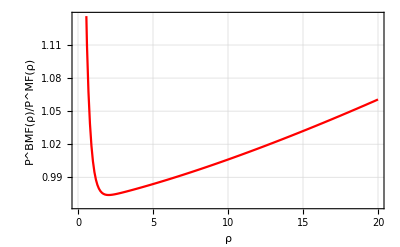

```mathematica
ListPlot[BMFtoMF,Frame->True,PlotStyle->{Directive[Red,PointSize[Medium]]},LabelStyle->Directive[FontFamily->"Helvetica",Medium],TicksStyle->Directive[FontFamily->"Helvetica",Medium],FrameLabel->{"ρ","P^BMF(ρ)/P^MF(ρ)"},PlotRange->Automatic,GridLines->Automatic,Joined->True]
```

### End of notebook